```mathematica
createCircle[height_, width_, radius_]:={height*Random[], width*Random[], radius}
```

```mathematica
addCircle[circleList_, height_, width_, radius_]:=
Module[{newCircle, d, overlap=0},
newCircle=createCircle[height, width, radius];
For[i=1, i≤Length[circleList],
d=Sqrt[(circleList[[i]][[1]]-newCircle[[1]])^2+(circleList[[i]][[2]]-newCircle[[2]])^2];
overlap =If[d<circleList[[i]][[3]] + newCircle[[3]],overlap + 1, overlap];
i++];
If[overlap==0, newCircle, {}]]
```

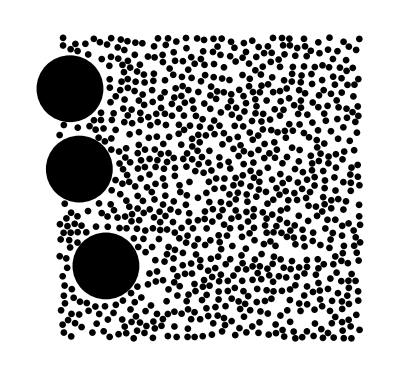
{0.369451,-Graphics-}

```mathematica
big=1;
small=0.1;
h=9;
circleList={createCircle[ L, L, big]}; 
newCircle=addCircle[circleList, L, L, small];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<10000,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, big, small]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
{rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))],Graphics[Disk[{#[[1]], #[[2]]}, #[[3]]]&/@newCircleList]}
```

```mathematica
runSimulation[iterations_, boxSize_, B_, S_, pB_]:=Module[{},
big=B;
small=S;
circleList={createCircle[ boxSize, boxSize, big]}; 
newCircle=addCircle[circleList, boxSize, boxSize, small];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<iterations,
circleList= newCircleList;
newCircle=addCircle[circleList, boxSize, boxSize,If[ Random[]≤ pB, big, small]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
{rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((boxSize+1)*(boxSize+1))],Graphics[Disk[{#[[1]], #[[2]]}, #[[3]]]&/@newCircleList]}]
```

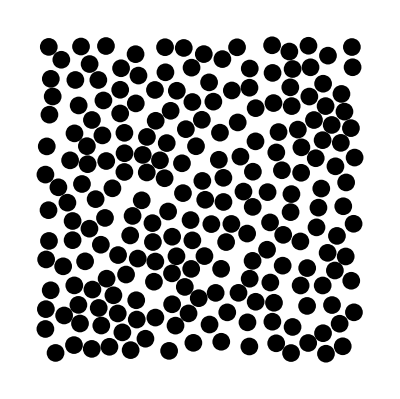
{0.523599,-Graphics-}

```mathematica
runSimulation[60000, 35, 1, 1, 0.9]
```

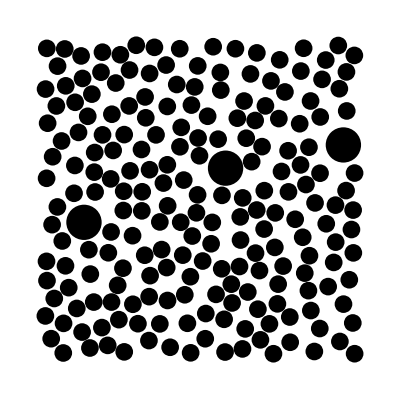
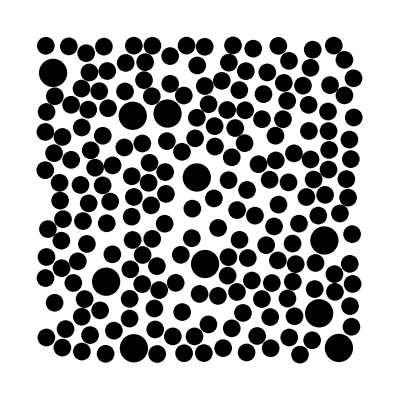
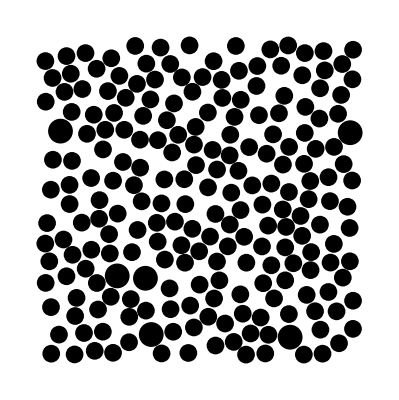
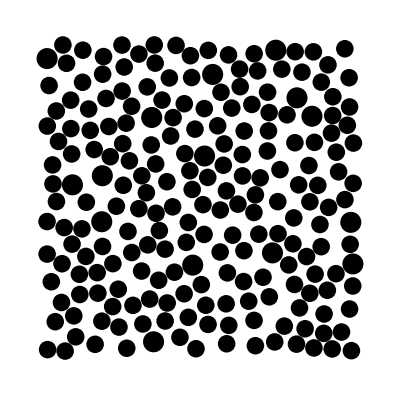
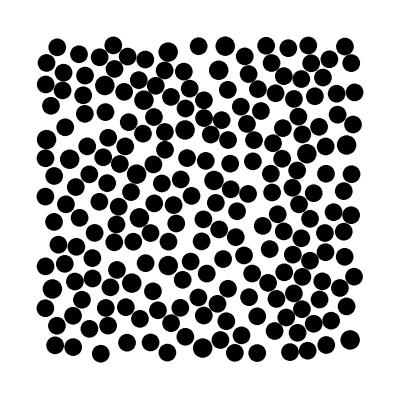
{{2,{0.528447,-Graphics-}},{1.6,{0.549294,-Graphics-}},{1.4,{0.544834,-Graphics-}},{1.2,{0.539598,-Graphics-}},{1.1,{0.53761,-Graphics-}}}

```mathematica
{#, runSimulation[60000, 35, 1, #, 0.9]}&/@{2, 1.6,1.4, 1.2, 1.1}
```

```mathematica
{#, runSimulation[#]}&/@{5000, 10000, 20000, 50000, 100000}
```

$Aborted

```mathematica
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))]
```

0.167284

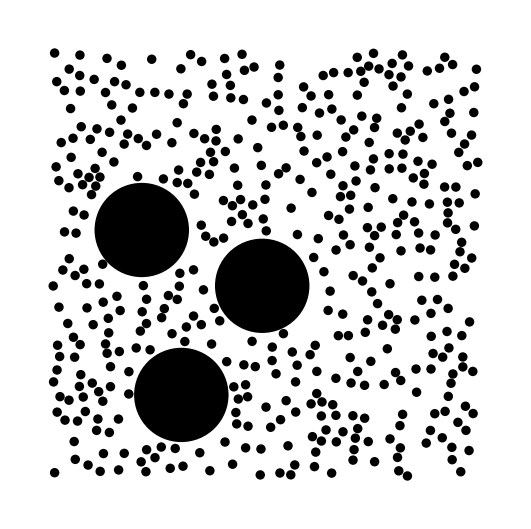

```mathematica
Graphics[Disk[{#[[1]], #[[2]]}, #[[3]]]&/@newCircleList]
```

```mathematica
11*11*0.5
```

60.5

```mathematica
N[Pi*20]
```

62.8319

This is the main program

```mathematica
L=24;
a=1;
b=0.2;
data={};
For[h=1, h<10, h++,
Print[h];
circleList={createCircle[ L, L, a]}; 
newCircle=addCircle[circleList, L, L, 1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<15000,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, a, b]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))];
data=Append[data, {1-h/10, rho, Length[Select[newCircleList, #[[3]]==a&]], Length[Select[newCircleList, #[[3]]==b&]]}];];
data
```

1

2

3

4

5

6

7

8

9

{{1/10,0.532412,92,348},{1/5,0.546084,86,566},{3/10,0.52819,73,802},{2/5,0.516327,65,943},{1/2,0.50929,57,1108},{3/5,0.473903,40,1357},{7/10,0.458019,32,1478},{4/5,0.461839,30,1547},{9/10,0.422431,12,1801}}

```mathematica
data
```

{{1/10,0.540354,89,74},{1/5,0.535327,71,142},{3/10,0.54538,69,158},{2/5,0.510195,54,190},{1/2,0.532814,48,232},{3/5,0.511451,41,243},{7/10,0.500142,28,286},{4/5,0.486319,21,303},{9/10,0.478779,7,353}}

```mathematica
data={};
For[h=1, h<3, h++,
L=24;
a=1;
b=0.5;
circleList={createCircle[ L, L, a]}; 
newCircle=addCircle[circleList, L, L, 1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList]
For[z=1, z<100,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, a, b]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))];
data=Append[data, {h/10, rho, Length[Select[newCircleList, #[[3]]==a&]], Length[Select[newCircleList, #[[3]]==b&]]}];]
```

{{4.06752,23.1461,1},{7.43894,19.6572,1}}

```mathematica
rho
```

0.503911

```mathematica
Length[newCircleList]
```

2120

```mathematica
25^2
```

625

```mathematica
Length[newCircleList]
```

15

```mathematica
newCircle
```

{}

```mathematica
cicleList={createCircle[10, 10, 1], createCircle[10, 10, 1]};
```

```mathematica
circleList
```

Hold[Append[circleList,{4.44644,4.63359,1}]]

```mathematica
Clear[cicleList]
```

```mathematica
circleList=0
```

0

```mathematica
circleList
```

0

```mathematica
circleList={createCircle[10,10,1], createCircle[10,10,1]}
```

{{6.45853,8.24283,1},{9.27809,2.1626,1}}

```mathematica
L=24;
a=1;
b=0.5;
circleList={createCircle[ L, L, a]}; 
newCircle=addCircle[circleList, L, L, 1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<100,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, a, b]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))];
Print[rho];
L=24;
a=1;
b=0.5;
circleList={createCircle[ L, L, a]}; 
newCircle=addCircle[circleList, L, L, 1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<100,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, a, b]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))];
Print[rho];
```

{{12.096,1.99401,1},{8.45818,10.885,1}}

$Aborted

{}

{{19.7928,20.0749,1},{20.7764,9.7605,1}}

```mathematica
Correlation[{0,0, 1, 1, 1, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0,0}]
```

7/15

```mathematica
?Sound
```

RowBox[{"Sound", "[", StyleBox["primitives", "TI"], "]"}] represents a sound. 
RowBox[{"Sound", "[", RowBox[{StyleBox["primitives", "TI"], ",", StyleBox["t", "TI"]}], "]"}] specifies that the sound should have duration StyleBox["t", "TI"].
RowBox[{"Sound", "[", RowBox[{StyleBox["primitives", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["t", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] specifies that the sound should extend from time SubscriptBox[StyleBox["t", "TI"], StyleBox["min", "TI"]] to time SubscriptBox[StyleBox["t", "TI"], StyleBox["max", "TI"]].